```mathematica
rawdata=Import["/Users/stevenschowalter/Desktop/phys191mms/Rb Data/428fstep5.txt","Data"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

80

```mathematica
freq=Take[rawdata,All,{1}];
signal=Take[rawdata,All,{2}];
```

```mathematica
plotdata=Take[rawdata,All,2];
```

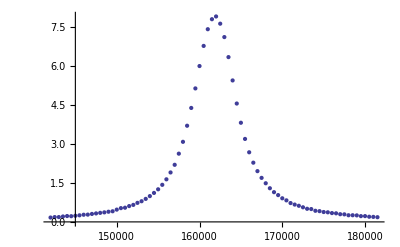

```mathematica
dataplot=ListPlot[plotdata]
```

```mathematica
Do[If[Max[signal]==signal[[i]][[1]],{Print[i,plotdata[[i]]],{max}=freq[[i]]}],{i,1,num}]
```

41{162000.,7.909}

```mathematica
model=g/(π (g^2+(x-x0)^2/b));
```

```mathematica
Needs["NonlinearRegression`"]
```

```mathematica
fitdata=NonlinearRegress[plotdata,model,{x0,g,b},x,MaxIterations->1000]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{3.47037×10^-17, -1.28177×10^-12, -1.28177×10^-12}, {« 1 »}, {0., 0., -« 23 »}} may contain significant numerical errors.

{BestFitParameters→{x0→6.31602×10^6,g→83.3115,b→83.3115},ParameterCITable→ | Estimate | Asymptotic SE | CI
x0 | 6.31602×10^6 | 1.05723×10^22 | {-2.10521×10^22,2.10521×10^22}
g | 83.3115 | 9.3741×10^24 | {-1.86662×10^25,1.86662×10^25}
b | 83.3115 | 9.3741×10^24 | {-1.86662×10^25,1.86662×10^25},EstimatedVariance→7.95737,ANOVATable→ | DF | SumOfSq | MeanSq
Model | 3 | 1.59365×10^-8 | 5.31217×10^-9
Error | 77 | 612.717 | 7.95737
Uncorrected Total | 80 | 612.717 | 
Corrected Total | 79 | 379.474 | ,AsymptoticCorrelationMatrix→(1. | -1. | 1.
-1. | 1. | -1.
1. | -1. | 1.),FitCurvatureTable→ | Curvature
Max Intrinsic | 3.14115×10^21
Max Parameter-Effects | 8.10498×10^36
95. % Confidence Region | 0.605967}

```mathematica
fit=model/.fitdata[[1]][[2]];
```

```mathematica
fitplot=Plot[fit,{x,100000,200000},PlotStyle->{Red, Thick}];
```

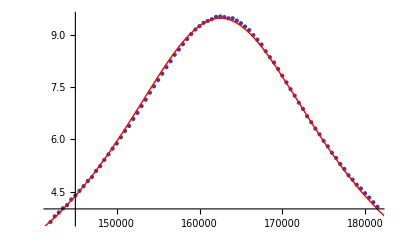

```mathematica
Show[dataplot,fitplot]
```